```mathematica
FR[θ_,a_]=2/Pi ArcTan[a/(2 Sin[θ/2]^3)]Sin[θ/2];
FRl[l_,a_]:=1/Pi NIntegrate[FR[θ,a]Cos[l*θ],{θ,0,Pi},MaxRecursion->10,PrecisionGoal->5];
F0[Ω_,α_]=(4-(3 HypergeometricPFQ[{1/2,5/6,7/6},{4/3,5/3},-4/(Ω^2 α^2)])/(Ω α))/(2 π);
f[Ω_,q_,α_,r_]=1-Ω/q r(1+(2F0[Ω,α])/q);
fm[Ω_,q_,α_,r_]:=r(1-2 FRl[1,Ω*α]/q r);
rp[Ω_,q_,α_]=(Ω+F0[Ω,α]+Sqrt[(Ω+F0[Ω,α])^2-q^2])/q;
rm[Ω_,q_,α_]=(Ω+F0[Ω,α]-Sqrt[(Ω+F0[Ω,α])^2-q^2])/q;
urenoml[l_,Ω_,q_,α_]:=1/(rp[Ω,q,α]-rm[Ω,q,α])(f[Ω,q,α,rm[Ω,q,α]]/rm[Ω,q,α]^(l+1)-f[Ω,q,α,rp[Ω,q,α]]/rp[Ω,q,α]^(l+1))
renorm[Ω_,q_,α_]:=1/Sqrt[1+2 Sum[Abs[urenoml[l,Ω,q,α]]^2,{l,1,1000}]];
UU[θ_,Ω_,q_,α_]:=renorm[Ω,q,α](1+2 Sum[urenoml[l,Ω,q,α]Cos[l θ],{l,1,100}])
zeromode[Ω_,q_,α_]:=Ω(Ω+2F0[Ω,α])-q^2;
zeromode1[Ω_,q_,α_]:=(Ω+2F0[Ω,α])rm[Ω,q,α]-q
shearmode[Ω_,q_,α_]:=4*FRl[1,Ω*α](Ω+F0[Ω,α]-FRl[1,Ω*α])-q^2
shearmode1[Ω_,q_,α_]:=q-2 *rm[Ω,q,α]*FRl[1,Ω*α]
shearmodethird[Ω_,q_,α_]:=q^2-2 q FRl[1,Ω*α] rm[Ω,q,α]-4 FRl[2,Ω*α](Ω+F0[Ω,α]-FRl[1,Ω*α])rm[Ω,q,α]^2
urenomlzero[l_,Ω_,q_,α_]:=-1/(rp[Ω,q,α]-rm[Ω,q,α])f[Ω,q,α,rp[Ω,q,α]]/rp[Ω,q,α]^(l+1);
urenomlShear[l_,Ω_,q_,α_]:=-1/(rp[Ω,q,α]-rm[Ω,q,α])fm[Ω,q,α,rp[Ω,q,α]]/rp[Ω,q,α]^(l+1);
renormzero[Ω_,q_,α_]:=1/Sqrt[1+2 Sum[urenomlzero[l,Ω,q,α]^2,{l,1,1000}]];
renormShear[Ω_,q_,α_]:=1/(Sqrt[2]Sqrt[1+ Sum[urenomlShear[l,Ω,q,α]^2,{l,2,1000}]]);
```

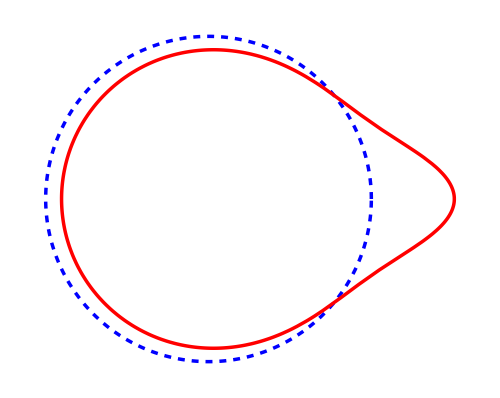

```mathematica
Clear[plz];(* -Graphics- *)
th=0.005;plz[kf_,α_]:=Module[{r1,r2,f2,barom,qbar=0.01,rem,utheta,om,alpha=α,check},
om=FindRoot[zeromode[barom,qbar,alpha]==0,{barom,0.1}][[1,2]];
check=F0[om,alpha]+om;
r1=rm[om,qbar,alpha];r2=rp[om,qbar,alpha];f2=f[om,qbar,alpha,r2];
rem=renormzero[om,qbar,alpha];
 If[check>qbar(* is s η > 1 ? *),PolarPlot[{kf,kf-0.75+rem(1-2*Sum[Cos[l θ](1/(r2-r1)f2/r2^(l+1)),{l,1,10^3}])},{θ,0,2π},PlotRange->{All,All},Frame->False,Axes->None,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,Bold},LabelStyle->Directive[Black,24,FontFamily->"LM Roman 10",Bold],FrameTicks->None,PlotStyle->{{Blue,Dashed,Thickness[th]},{Red(* Hue[α]*),Thickness[th]}},MaxRecursion->5,ImageSize->500],Print["False"]]
]
pl=plz[5,0.1]
SetDirectory[NotebookDirectory[]];
Export["0.png",Rasterize[pl,ImageResolution-> 500,Background->None],ImageSize->500];
```

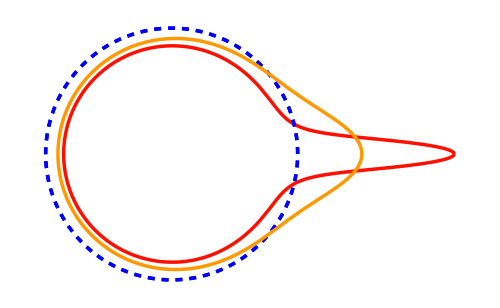

```mathematica
tot=Show[plz[5,0.01],plz[5,0.1]]
SetDirectory[NotebookDirectory[]];
(*Export["zeromode_shape.pdf",Rasterize[tot,ImageResolution-> 500],ImageSize->500];*)
```